```mathematica
(*
First I want to figure out at what points the partition function goes negative because the Gibbs' free energy goes as
-> G = - k T Log[Z] --> G is analytic means Z must be positive ....
As a first step, I would want to figure out potential submodules/functions which can go negative ....
*)
```

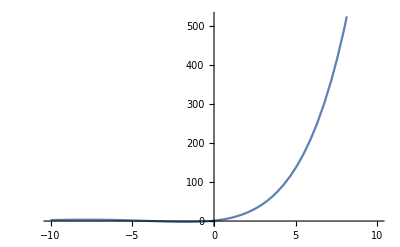

```mathematica
Plot[HypergeometricPFQ[{1},{1/3,2/3},x],{x,-10,10}]
```

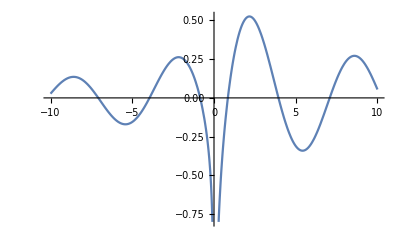

```mathematica
Plot[Re[BesselJ[1/3,x]-BesselJ[-1/3,x]],{x,-10,10}]
```

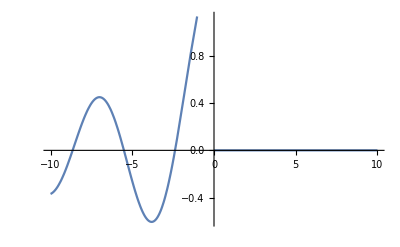

```mathematica
Plot[Im[BesselJ[1/3,x]-BesselJ[-1/3,x]],{x,-10,10}]
```

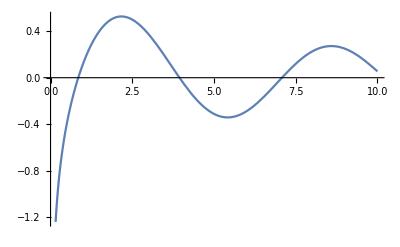

```mathematica
Plot[Re[BesselJ[1/3,x]-BesselJ[-1/3,x]],{x,0,10}]
```

```mathematica
Manipulate[
Plot[Log[Cosh[k x]-Cosh[x]],{x,0,10}],{k,1.1,10}
]
```

```mathematica
(* Some of the summation terms are to be computed using Monte Carlo sampling .... *)
```

```mathematica
(1.6*10^(-19))^2/(4π (8.85*10^(-12))*(419.10*10^(-12))^2)
```

1.31054×10^-9

```mathematica
Block[
{n=10,a=419.10*10^(-12),k=1.38*10^(-12),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=1},
Print[q E0 a/2/k/T];
Print[(k T/P/V0 n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])];
]
```

20.2464

267.263

```mathematica
Series[n^(2/3)/Gamma[n/2+1]^2 ,{n,Infinity,1}]//FullSimplify
```

ⅇ^((1+Log[2]-Log[n]) n+O[1/n]^3) ((1/n)^(1/3)/π-(1/n)^(4/3)/(3 π)+O[1/n]^(11/6))

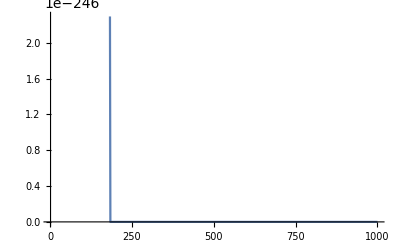

```mathematica
Plot[n^(2/3)/Gamma[n/2+1]^2,{n,1,1000}]
```

```mathematica
Block[
{n=10^4,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=1},
Print[q E0 a/2/k/T];
Print[(k T/P/V0 n^(2/3)/Gamma[n/2+1]^2 (Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])];
]
```

2.02464×10^12

9.4281161951343606559985101`15.954589770191005*^36128835332198

```mathematica
Block[
{n=10^4,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=1},
Print[n k T Log[n]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]]]
]
```

-3.44405×10^-7

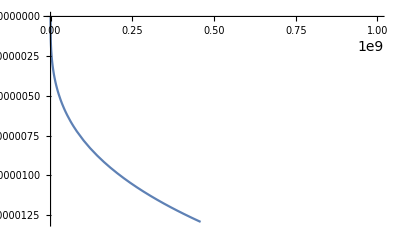

```mathematica
Block[
{a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=1},
Plot[-k T Log[Cosh[q E0 a(2n^(1/3)-1)/2/k/T]],{n,10,10^9}]
]
```

```mathematica
Block[
{n=4.5*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n]-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]]]
]
```

-0.0000128296

```mathematica
Block[
{n=4.5*10^3,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n]-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]]]
]
```

-2.60004×10^-7

```mathematica
Block[
{n=4.5*10^3,a=419.10*10^(-12),k=1.38*10^(-23),T=1000,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n]-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]]]
]
```

-2.60004×10^-7

```mathematica
Block[
{n=4.5*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^6,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n]-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]]]
]
```

-0.0000128296

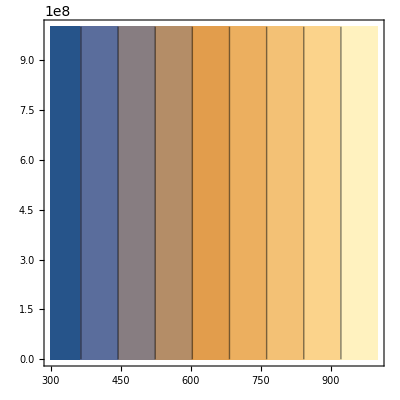

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T,P,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
ContourPlot[n k T Log[n]-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]],{T,300,1000},{P,10^5,10^9}]
]
```

```mathematica
Block[
{a=419.10*10^(-12),k=1.38*10^(-23),T=600,P=10^7,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(23)},
Print[-k T Log[k T/P/V0]-k T Log[Cosh[q E0 a/2/k/T]]]
]
```

-8.382×10^-9

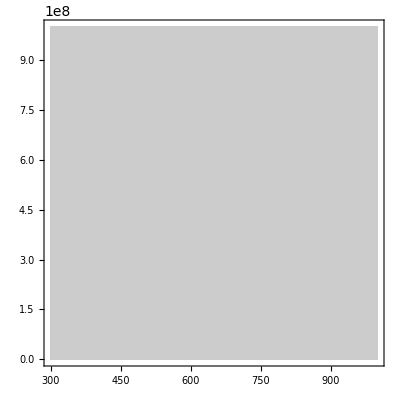

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T,P,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
ContourPlot[-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]],{T,300,1000},{P,10^5,10^9}]
]
```

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T,P,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Plot3D[n k T Log[n]-k T Log[k T/P/V0]-k T Log[(Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T]],{T,300,1000},{P,10^5,10^9}]
]
```

-Graphics3D-

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]
]
```

6.054449259503825014568113572`15.954589770191005*^1352807999720624

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T=600,P=10^6,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]
]
```

7.7126961377565318675622352021169834`15.954589770191005*^676403999860304

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T=300,P=10^5,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]]
]
```

5893.43

```mathematica
Block[
{n=4.57*10^8,a=419.10*10^(-12),k=1.38*10^(-23),T=600,P=10^6,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]]
]
```

5893.43

```mathematica
Block[
{n=100,a=419.10*10^(-12),k=1.38*10^(-23),T=600,P=10^6,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[Log[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]]
]
```

7.372897971778644610879097603×10^12

```mathematica
Block[
{n=10^5,a=419.10*10^(-12),k=1.38*10^(-23),T=1000,P=10^6,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Print[n k T Log[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]]
]
```

0.0761352

```mathematica
Block[
{n=10^5,a=419.10*10^(-12),k=1.38*10^(-23),T,P,q=1.6*10^(-19),E0=2.5*10^20,V0=10^(-6)},
Plot3D[n k T Log[n^(2/3) k T/P/V0 ((Cosh[q E0 a(2n^(1/3)-1)/2/k/T]-Cosh[q E0 a/2/k/T])/Sinh[q E0 a/2/k/T])]-0.0761352,{T,280,1000},{P,10^5,10^7}]
]
```

-Graphics3D-